3/19/22  Notebook for comparing the two methods for calculating energy of a 2-sphere system stored as potential energy.  Author: Jack Adams

```mathematica
ClearAll["Global`*"];
a = 1. 10^-3; 
q1 = 10^-12;
eps0= 8.85 * 10^-12; 
JoulesToEV = 6.2415093433 * 10^18;
numElements = 20;
xList = Table[  ( 2a  + a (i-1)  ), {i,1, numElements}]
totalInteractionEnergy= Table[{0,0}, {i,1, numElements}];
totalInteractionEnergynJ= Table[{0,0}, {i,1, numElements}];
```

{0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021}

```mathematica
qEnclosed[r_]:= If[r < a,0., q1]   (* Hollow Sphere of Charge *)
(*  qEnclosed[r_]= If[r < a, 0., q1]     Hollow Sphere of Charge *)
```

```mathematica
(*  If[r<a,0.,q1] *)
```

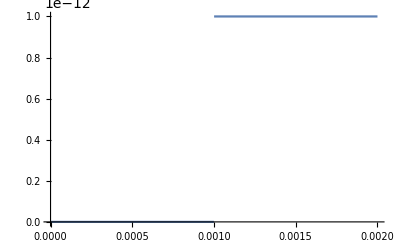

```mathematica
Plot[qEnclosed[r] ,{r,0, 2 a}]
```

```mathematica
eMag1[x_, y_, z_] := qEnclosed[  Sqrt[x^2 + y^2 + z^2] ]/(4 π eps0(x^2+ y^2 + z^2)) ;
```

```mathematica
eFieldCart1[x_, y_, z_] := eMag1[x, y, z] { x/Sqrt[x^2 + y^2 + z^2], y/Sqrt[x^2 + y^2 + z^2], z/Sqrt[x^2 + y^2 + z^2]};
eMag2[x_, y_, z_] := qEnclosed[  Sqrt[(x-xList[[n]])^2 + y^2 + z^2] ]/(4 π eps0( (x-xList[[n]])^2+ y^2 + z^2)) ;

eFieldCart2[x_, y_, z_] := eMag2[x, y, z] { (x-xList[[n]])/Sqrt[(x-xList[[n]])^2 + y^2 + z^2], y/Sqrt[(x-xList[[n]])^2 + y^2 + z^2], z/Sqrt[(x- xList[[n]])^2 + y^2 + z^2]} ;

interactionEnergyDensity[x_, y_, z_]  := eps0 Dot[eFieldCart1[x, y, z],eFieldCart2[x, y, z]];
```

```mathematica
n = 1;
```

```mathematica
While[n<numElements+1, 
xMid = xList[[n]] / 2.0;
totalInteractionEnergy[[n]] = { xList[[n]], Re[NIntegrate[  8  interactionEnergyDensity[x, y, z] , {x,xMid, ∞}, {y,0, ∞}, {z,0, ∞}, PrecisionGoal->7, Method->{"GlobalAdaptive","MaxErrorIncreases"->10000,Method->"GaussKronrodRule"}  ]]};
totalInteractionEnergynJ[[n]]= {xList[[n]],totalInteractionEnergy[[n]][[2]]* 10^12};
Print[ totalInteractionEnergy[[n]]  ];
n++ 
]
```

{0.002,4.4959×10^-12}

{0.003,2.99727×10^-12}

{0.004,2.24795×10^-12}

{0.005,1.79836×10^-12}

{0.006,1.49863×10^-12}

{0.007,1.28454×10^-12}

{0.008,1.12398×10^-12}

{0.009,9.99089×10^-13}

{0.01,8.9918×10^-13}

{0.011,8.17437×10^-13}

{0.012,7.49317×10^-13}

{0.013,6.91677×10^-13}

{0.014,6.42272×10^-13}

{0.015,5.99454×10^-13}

{0.016,5.61988×10^-13}

{0.017,5.2893×10^-13}

{0.018,4.99545×10^-13}

{0.019,4.73253×10^-13}

{0.02,4.4959×10^-13}

{0.021,4.28181×10^-13}

#### First, the enclosed charge, included needed constant of integration. Then the Electric field. Easier using just r, not cartesian.

```mathematica
(* qEnclosed1[r_]:= If[r < a,0., q1];  *)
eField1[r_] := qEnclosed[r]/(4 π r^2 eps0);
potSphereTEMP[r_] = -Integrate[eField1[r], r ]
potInfinity = Limit[potSphereTEMP[r], {r -> ∞} ]
potSphere1[r_] := potSphereTEMP[r] - potInfinity 
q1 * potSphere1[0.04]
```

-(Piecewise[{{0., r≤0.001}, {8.9918-0.0089918/r, True}}])

-8.9918

2.24795×10^-13

(TraditionalForm`Q)_2ϕ_1

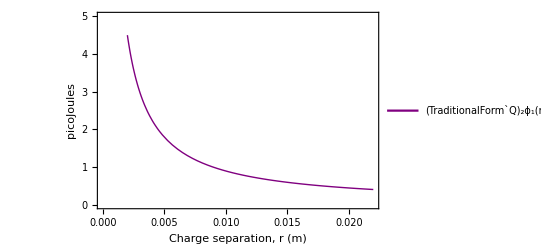

```mathematica
SubScripts = StringForm["````", Subscript["TraditionalForm`Q","2"],Subscript["ϕ","1"]]
legendsa={StringForm["````", SubScripts, "(r)"]};Plot1 = Plot[potSphere1[r]* q1  * 10^12,{r,2a,22 a}, FrameLabel-> {"Charge separation, r (m)", "picoJoules"}, PlotRange->{{0., 22a},{0,5.}},Frame->True, LabelStyle->Directive[Black, FontSize -> 14], PlotStyle->{{Thick,Purple}}, PlotLegends->Placed[legendsa,{Right, Center}], ImageMargins->10]
```

```mathematica
legends={StringForm["````dv","∫",Subscript["w","int"]]};Plot2 = ListPlot[totalInteractionEnergynJ, PlotMarkers->{"●"},
PlotRange->{{0., 22a},{0,5.}},Frame->True,  PlotStyle-> Blue,  LabelStyle->Directive[Black, FontSize -> 14], PlotLegends->Placed[{legends},{Right, Center}], Frame->True ]
```

-Graphics-

```mathematica
Show[Plot1, Plot2]
```

-Graphics-